```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

```mathematica
sne=Import["data/neordered.txt","Table"];
```

```mathematica
sne[[1]]
```

{0.00819005,2.00852}

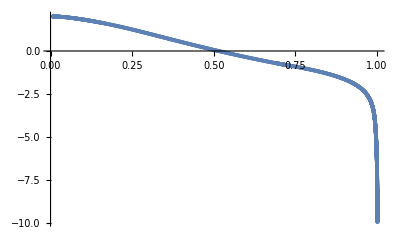

```mathematica
sneplt=Table[sne[[i]],{i,200,Length@sne-1800}];
snepl=ListPlot[sne,PlotRange->Full,ImageSize->Full]
```

```mathematica
fitted=LinearModelFit[sneplt,x,x]
```

FittedModel[2.2901-4.33005 x]

```mathematica
fittedPlt=Plot[Normal@fitted,{x,0,1}];
```

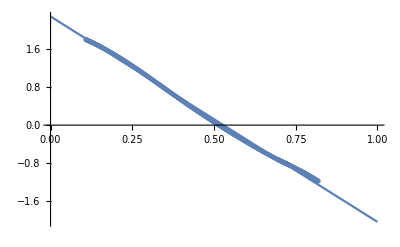

```mathematica
Show[fittedPlt,snepl,ImageSize->Full]
```

```mathematica
solMSW=Solve[2c s ==Sin[2 Subscript[θ, v]]/Sqrt[Δ̂+1-2 Δ̂ Cos[2 Subscript[θ, v]]]&&c^2-s^2== (Cos[2 Subscript[θ, v]]-Δ̂)/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{c,s}]//FullSimplify
```

{{c→(√((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→1/(√2 √(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))Csc[2 θ_v] √(1+Δ̂-2 Cos[2 θ_v] Δ̂) √((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))},{c→-(√((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→1/(√2 √(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))Csc[2 θ_v] √(1+Δ̂-2 Cos[2 θ_v] Δ̂) √((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))},{c→-(√((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→-1/(√2 √(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))Csc[2 θ_v] √(1+Δ̂-2 Cos[2 θ_v] Δ̂) √((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))},{c→(√((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2),s→1/(√2 √(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))Csc[2 θ_v] √(1+Δ̂-2 Cos[2 θ_v] Δ̂) √((Cos[2 θ_v]-Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂+√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))}}

```mathematica
c/.solMSW[[1]]
s/.solMSW[[1]]
```

(√((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))))/(√2)

1/(√2 √(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))Csc[2 θ_v] √(1+Δ̂-2 Cos[2 θ_v] Δ̂) √((Cos[2 θ_v]-Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))/(√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2))) (-Cos[2 θ_v]+Δ̂-√(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2) √(1+(1/(1+Δ̂-2 Cos[2 θ_v] Δ̂)-1/(1-2 Cos[2 θ_v] Δ̂+(Δ̂)^2)) Sin[2 θ_v]^2))

```mathematica
Series[D[c/.solMSW[[1]],Δ̂],{Δ̂,0,0}]//FullSimplify
Series[D[c/.solMSW[[1]],Δ̂],{Δ̂,0,1}]//FullSimplify
Series[D[s/.solMSW[[1]],Δ̂],{Δ̂,0,1}]//FullSimplify
```

1/2 Cos[θ_v]^2 √(-Sin[θ_v]^2)+O[Δ̂]^1

1/2 Cos[θ_v]^2 √(-Sin[θ_v]^2)+1/8 Cos[θ_v]^2 (14-9 Cos[2 θ_v]+Cos[4 θ_v]) √(-Sin[θ_v]^2) Δ̂+O[Δ̂]^2

3/4 √(-Sin[θ_v]^2) Sin[2 θ_v]-1/8 ((-6+47 Cos[2 θ_v]-Cos[4 θ_v]) Cot[θ_v] (-Sin[θ_v]^2)^(3/2)) Δ̂+O[Δ̂]^2

```mathematica
Series[Sin[2 Subscript[θ, v]]/Sqrt[Δ̂+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{Δ̂,0,1}]
Series[(Cos[2 Subscript[θ, v]]-Δ̂)/Sqrt[(Δ̂)^2+1-2 Δ̂ Cos[2 Subscript[θ, v]]],{Δ̂,0,1}]
```

Sin[2 θ_v]+(-1/2 Sin[2 θ_v]+Cos[2 θ_v] Sin[2 θ_v]) Δ̂+O[Δ̂]^2

Cos[2 θ_v]+(-1+Cos[2 θ_v]^2) Δ̂+O[Δ̂]^2

```mathematica
(-1)^(3/2)
```

-ⅈ